```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Energy control

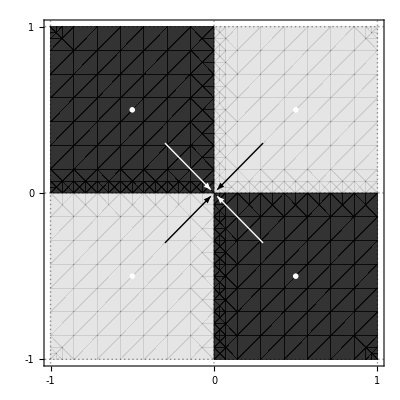

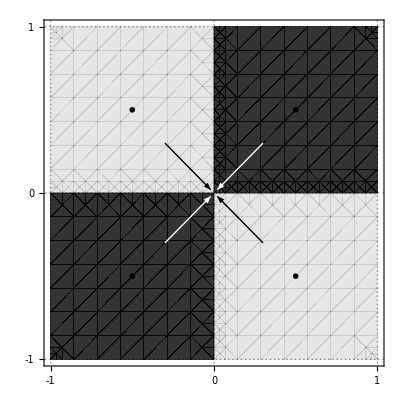

```mathematica
energyControl1 = ContourPlot[x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Text[MaTeX["+a_{max}",Magnification->2], {.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {-.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, .5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl2 = ContourPlot[-x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Text[MaTeX["+a_{max}",Magnification->2], {-.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, .5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, -.5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control1.pdf",energyControl1,"PDF"]
Export[NotebookDirectory[]<>"../energy-control2.pdf",energyControl2,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control2.pdf

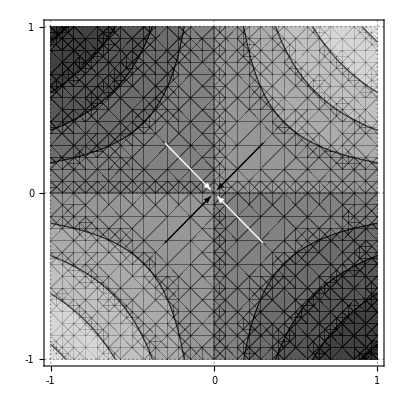

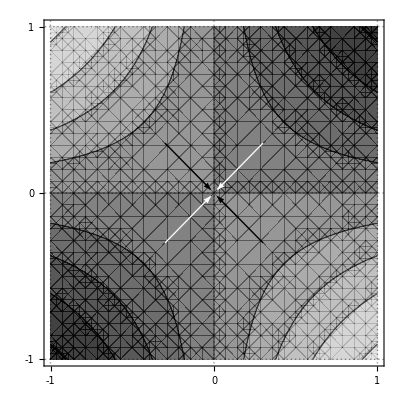

```mathematica
energyControl3 = ContourPlot[Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl4 = ContourPlot[-Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control3.pdf",energyControl3,"PDF"]
Export[NotebookDirectory[]<>"../energy-control4.pdf",energyControl4,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control3.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control4.pdf

## Cogging Torque

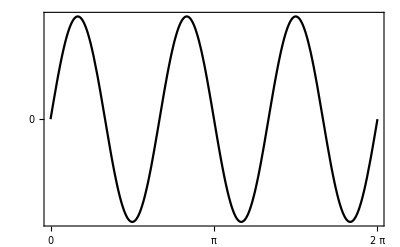

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{MaTeX["\\text{Angolo}",Magnification->1.5], MaTeX["\\text{Coppia}",Magnification->1.5]},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf

## Simulation

```mathematica
v2 = (x'[t] + l θ'[t]*Cos[θ[t]])^2 + ( l θ'[t]*Sin[θ[t]])^2;
T = 1/2 *M*x'[t]^2       + 1/2* m*v2    + 1/2*(J - m l^2)*θ'[t]^2 ;
V = m*g*l*Cos[θ[t]];
L = T - V;

e1 =D[D[L, x'[t]], t] - D[L, x[t]] == +u[t];
e2 = D[D[L, θ'[t]], t] - D[L, θ[t]] ==0 //Simplify;
motionEquations = Simplify[Solve[e1 && e2, {x''[t], θ''[t]}]][[1]];

params = {
	g ->9.8,
	l -> .38,
	m -> .15,
	M -> .175,
J->.1,
r11->1,
q11->1
};
```

```mathematica
Simplify[Solve[e1, { x''[t]}]][[1]] //TraditionalForm 
Simplify[Solve[e2, { θ''[t]}]][[1]] //TraditionalForm
motionEquations[[1, 2]]//Simplify//TraditionalForm
motionEquations[[2, 2]] //Simplify // TraditionalForm
```

{x''(t)→(-l m θ''(t) cos(θ(t))+l m (θ'(t))^2 sin(θ(t))+u(t))/(m+M)}

{θ''(t)→(l m (g sin(θ(t))-cos(θ(t)) x''(t)))/J}

(l m sin(θ(t)) (J (θ'(t))^2-g l m cos(θ(t)))+J u(t))/(J (m+M)-l^2 m^2 cos^2(θ(t)))

(l m (sin(θ(t)) (l m (θ'(t))^2 cos(θ(t))-g (m+M))+u(t) cos(θ(t))))/(l^2 m^2 cos^2(θ(t))-J (m+M))

```mathematica
ssm = StateSpaceModel[
	{e1, e2},
	{
    {x[t],0},
		{x'[t], 0},
		{θ[t], 0},
		{θ'[t], 0}
	},
	{u[t]},
	{θ[t], x[t], θ'[t]},
	t
]  //Simplify;
A = ssm[[1, 1]];
B = ssm[[1, 2]];

Q = ResourceFunction["HessianMatrix"][T-V, {x[t], x'[t],θ[t], θ'[t]}]  /. {x[t] -> 0, x'[t] ->0, θ[t] -> 0, θ'[t] -> 0};
Q +=  DiagonalMatrix[{q11, 0, 0, 0}];
R = DiagonalMatrix[{r11}];
```

```mathematica
A//MatrixForm
B//MatrixForm
{B, A.B, A.A.B, A.A.A.B} //MatrixForm
Q//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | (g l^2 m^2)/(l^2 m^2-J (m+M)) | 0
0 | 0 | 0 | 1
0 | 0 | -(g l m (m+M))/(l^2 m^2-J (m+M)) | 0)

(0
J/(-l^2 m^2+J (m+M))
0
(l m)/(l^2 m^2-J (m+M)))

((0) | (J/(-l^2 m^2+J (m+M))) | (0) | ((l m)/(l^2 m^2-J (m+M)))
(J/(-l^2 m^2+J (m+M))) | (0) | ((l m)/(l^2 m^2-J (m+M))) | (0)
(0) | ((g l^3 m^3)/((l^2 m^2-J (m+M))^2)) | (0) | (-(g l^2 m^2 (m+M))/((l^2 m^2-J (m+M))^2))
((g l^3 m^3)/((l^2 m^2-J (m+M))^2)) | (0) | (-(g l^2 m^2 (m+M))/((l^2 m^2-J (m+M))^2)) | (0))

(q11 | 0 | 0 | 0
0 | m+M | 0 | l m
0 | 0 | g l m | 0
0 | l m | 0 | J)

```mathematica
eqnsNonLinear = {
e1, e2,
	x[0] == x'[0] == θ'[0] == 0, θ[0] ==.1
} /. params /. u[t]->0;
T=5;
solsN =  NDSolve[eqnsNonLinear, {x, θ}, {t, 0, T}];
```

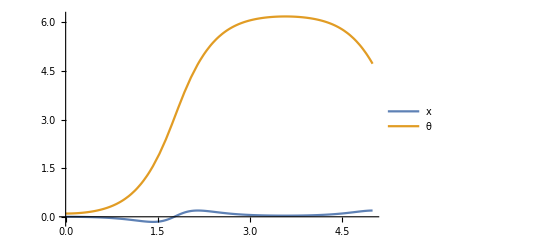

```mathematica
Plot[Evaluate[{x[t], θ[t]} /.  solsN], {t, 0, T},PlotLegends->{x, θ}]
```

```mathematica
K = LQRegulatorGains[ssm /. params, {Q, R} /. params];
```

{{-1.,-1.62938,-16.194,-6.70826}}

```mathematica
K // MatrixForm
A-B.K /. params //Eigenvalues
```

(-1. | -1.62938 | -16.194 | -6.70826)

{-2.46651+0.275595 ⅈ,-2.46651-0.275595 ⅈ,-1.28434+1.20449 ⅈ,-1.28434-1.20449 ⅈ}

```mathematica
s[t_] = {x[t],  x'[t], θ[t], θ'[t] };
uControl = {u[t] ->- Klqr.(s[t])};

eqnsControlLQR = {
	e1, e2,
	x[0] ==.05, x'[0] == θ'[0] == 0, θ[0] ==.05
} /. params /. uControl;

T = 5;
solsN =  NDSolve[eqnsControlLQR, {x, θ}, {t, 0, T}];
```

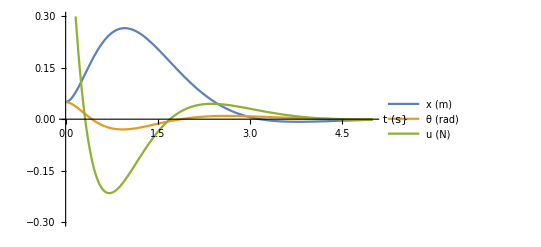

```mathematica
lqrPlot = Plot[Evaluate[{x[t], θ[t], u[t]/.uControl} /.  solsN], {t, 0,T},PlotLegends->{"x (m)", "θ (rad)", "u (N)"}, PlotRange->{-.3, .3}, AxesLabel->{"t (s}"}]
(*NIntegrate[powerLQR, {t, 0, T}]*)
```

```mathematica
poles = {-1, -1.1, -1.2, -1.3};
Ksub = StateFeedbackGains[ssm,poles] /. params;
```

```mathematica
(A-B.Ksub) /. params //Eigenvalues
```

{-1.3,-1.2,-1.1,-1.}

```mathematica
s[t_] = {x[t],  x'[t], θ[t], θ'[t] };
uControl = {u[t] ->- Ksub.(s[t])};

eqnsControlLQR = {
	e1, e2,
	x[0] ==.05, x'[0] == θ'[0] == 0, θ[0] ==.05
} /. params /. uControl;

T = 8;
solsN =  NDSolve[eqnsControlLQR, {x, θ}, {t, 0, T}];
```

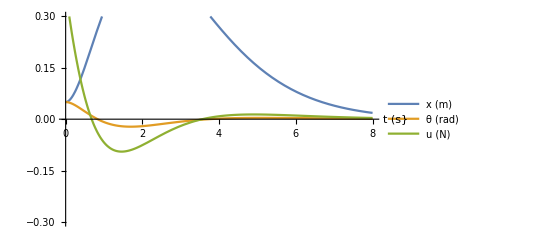

{{0.0357861}}

```mathematica
lqrPlot = Plot[Evaluate[{x[t], θ[t], u[t]/.uControl} /.  solsN], {t, 0,T},PlotLegends->{"x (m)", "θ (rad)", "u (N)"}, PlotRange->{-.3, .3}, AxesLabel->{"t (s}"}]
(*NIntegrate[powerSub, {t, 0, T}]*)
```